```mathematica
GradientDescent[{X0_,Y0_}, func_,ϵ_]:=Module[{point,direction,step,points={},funcvalues={},norms={},stepvalues={},funcprevpoint,funcpoint,criteria },
point= {X0,Y0};
AppendTo[points,point];
AppendTo[funcvalues,func[point]];
criteria =ϵ+1;
While [criteria >ϵ,
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
AppendTo[norms,Norm[direction]];
step = NArgMin[func[point + α*direction],α];
AppendTo[stepvalues,step];
funcprevpoint=func[point];
point = point + step * direction;
funcpoint = func[point];
AppendTo[points,point];
AppendTo[funcvalues,funcpoint];
criteria = Norm[funcpoint-funcprevpoint] ;
(*Norm[direction] Критерий через норму градиента*)
];
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
AppendTo[norms,Norm[direction]];
step = NArgMin[func[point + α*direction],α];
AppendTo[stepvalues,step];

{points}~Join~{funcvalues}~Join~{norms}~Join~{stepvalues}
];
```

```mathematica
GradientDescent[{X0_,Y0_}, func_,{γ_,ω_}]:=Module[{point,direction ,step ,points={},funcvalues={},norms={},stepvalues={},funcprevpoint ,funcpoint = 0},
point= {X0,Y0};
AppendTo[points,point];
AppendTo[funcvalues,func[point]];
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
(*первый раз решаем задачу одномерной минимизации*)
step = 1/Norm[direction];
(*входим в while*)
funcprevpoint =ω*step*(Norm[direction])^2 + 1;
While [Abs[funcprevpoint-funcpoint]>ω*step*(Norm[direction])^2,
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
AppendTo[norms,Norm[direction]];
(*остальные разы умножаем на γ*)
step =γ * step;
AppendTo[stepvalues,step];
funcprevpoint=func[point];
point = point + step * direction;
funcpoint = func[point];
AppendTo[points,point];
AppendTo[funcvalues,funcpoint];
];
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
AppendTo[norms,Norm[direction]];
step = step*γ;
AppendTo[stepvalues,step];

{points}~Join~{funcvalues}~Join~{norms}~Join~{stepvalues}
]
```

```mathematica
eps = 10^(-3);
params = {0.5, 0.005};
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

```mathematica
Res=GradientDescent[{-1,-2}, rosenbrok,eps];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
κArray = Res[[4]];
func=rosenbrok;
setX = {x,-2,2};
setY ={y,-4,4};
Print[points[[-1]]];
```

{0.935662,0.832467}

```mathematica
Res=GradientDescent[{-2 √5,1}, f,eps];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
κArray = Res[[4]];
func=f;
setX = {x,-4,0};
setY ={y,-8,0};
Print[points[[-1]]];
```

{-2.2377,-4.46814}

```mathematica
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,(*траектория поиска точки минимума*)Epilog->{Purple,Thickness[0.001],Arrowheads[.04],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
```

-Graphics-

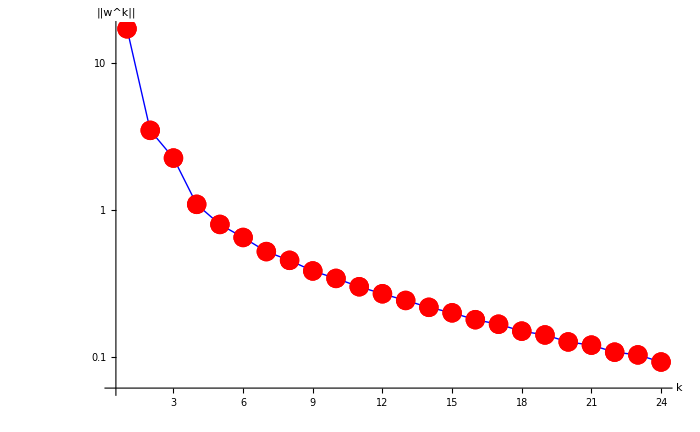

```mathematica
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
gridLabel={"k","(X^k)","f(X^k)","κ_k","||w^k||"};
gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"]
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение шага спуска*)
gridData[[All,4]]=SetAccuracy[κArray,4];
(*в 5-м столбце-значение нормы невязки*)
gridData[[All,5]]=SetAccuracy[norms,4];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
table=Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | (X^k) | f(X^k) | κ_k | ||w^k||
0 | ( -1.000, -2.000 ) | 13. | 0.086 | 17.09
1 | ( 0.379, -1.483 ) | 3.031 | 0.335 | 3.474
2 | ( -0.030, -0.394 ) | 1.216 | 0.294 | 2.25
3 | ( 0.590, -0.162 ) | 0.428 | 0.258 | 1.089
4 | ( 0.491, 0.102 ) | 0.278 | 0.272 | 0.794
5 | ( 0.693, 0.178 ) | 0.186 | 0.233 | 0.648
6 | ( 0.640, 0.319 ) | 0.138 | 0.243 | 0.519
7 | ( 0.758, 0.363 ) | 0.103 | 0.219 | 0.452
8 | ( 0.723, 0.456 ) | 0.081 | 0.223 | 0.383
9 | ( 0.803, 0.486 ) | 0.064 | 0.211 | 0.341
10 | ( 0.778, 0.553 ) | 0.052 | 0.21 | 0.299
11 | ( 0.837, 0.575 ) | 0.042 | 0.204 | 0.268
12 | ( 0.818, 0.627 ) | 0.035 | 0.2 | 0.241
13 | ( 0.863, 0.643 ) | 0.029 | 0.2 | 0.217
14 | ( 0.848, 0.684 ) | 0.024 | 0.193 | 0.199
15 | ( 0.884, 0.697 ) | 0.02 | 0.196 | 0.178
16 | ( 0.871, 0.730 ) | 0.017 | 0.187 | 0.166
17 | ( 0.900, 0.741 ) | 0.015 | 0.193 | 0.149
18 | ( 0.890, 0.768 ) | 0.013 | 0.182 | 0.14
19 | ( 0.914, 0.777 ) | 0.011 | 0.191 | 0.126
20 | ( 0.906, 0.800 ) | 0.009 | 0.179 | 0.12
21 | ( 0.926, 0.807 ) | 0.008 | 0.189 | 0.107
22 | ( 0.919, 0.826 ) | 0.007 | 0.175 | 0.103
23 | ( 0.936, 0.832 ) | 0.006 | 0.188 | 0.092